```mathematica
Clear["Global`*"];
```

```mathematica
$Version
```

12.1.0 for Linux x86 (64-bit) (March 14, 2020)

# Demo file for ManeParse Package Version 5.0

### Version 5.0 18 October 2019 Comments and questions to: Eric Godat egodat@smu.edu Ben Clark dbclark@smu.edu Fred Olness olness@physics.smu.edu

## Set Directory

#### This example notebook is written with relative directories and is intended to be run within the folder extracted from the tarball. Uncomment and modify the code below to set a different directory for the LHA files.

```mathematica
(* This just drops the leading path info to make the list of files easier to read *)
dropPath=Take[(FileNameSplit /@ # ) //Transpose,-1][[1]]&;
```

```mathematica
NotebookDirectory[];
here=NotebookDirectory[]
```

C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\

```mathematica
(* If there is a problem with the Mathematica working directory, 
you can enter it manually here *)
SetDirectory[here]
```

C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo

```mathematica
(* This shows what files should be in this main directory *)
FileNames["*.*",here] //dropPath
```

{Demo5.nb,Demo5.pdf,figs4paper_v5.nb,figs4paper_v5.pdf,MakeDemo.py,ManeParse_v2.pdf,manual_v5.nb,manual_v5.pdf,noe2.perl,User.pdf}

## Setup Other Directories

```mathematica
dirPackages=here<>"/MP_packages";
```

```mathematica
dirFilesLHA=here<>"./PDFDIR/LHA";
dirCT10=dirFilesLHA<>"/CT10";
dirMSTW=dirFilesLHA<>"/MSTW2008lo68cl";
dirNNPDF=dirFilesLHA<>"/NNPDF30_nlo_as_0118";
FileNames["*",dirFilesLHA] //dropPath
```

{CT10,MSTW2008lo68cl,NNPDF30_nlo_as_0118}

```mathematica
dirFilesPDS=here<>"./PDFDIR/PDS";
dirCT10pds = dirFilesPDS<>"/ct10.pds";
dirCTEQ66 = dirFilesPDS<>"/ctq66m.pds";
FileNames["*",dirFilesPDS] //dropPath
```

{ct10.pds,ctq66m.pds}

```mathematica
dirPackages
FileNames["*",dirPackages]//dropPath
```

/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo//MP_packages

{pdfCalc.m,pdfErrors.m,pdfParseCTEQ.m,pdfParseLHA.m,README_V05.TXT}

```mathematica
FileNames["*.dat",dirCT10]//dropPath //Short
```

{CT10_0000.dat,CT10_0001.dat,CT10_0002.dat,CT10_0003.dat,CT10_0004.dat,CT10_0005.dat,«42»,CT10_0048.dat,CT10_0049.dat,CT10_0050.dat,CT10_0051.dat,CT10_0052.dat}

## Load the package

#### Loading the main package provides many useful functions

```mathematica
Get[dirPackages<>"/pdfParseLHA.m"]
```

Version: pdfCalc 5.0

Version: ManeParse 5.0: April 2021

- Required Package: pdfCalc --Loaded -

===============================================================

- pdfParseLHA -

Version:  5.0: April 2021

Authors: E.J. Godat, D.B. Clark & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

```mathematica
Get[dirPackages<>"/pdfParseCTEQ.m"]
```

===============================================================

- pdfParseCTEQ -

Version:  5.0:  April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

```mathematica
Get[dirPackages<>"/pdfErrors.m"]
```

===============================================================

- pdfErrors -

Version:  5.0; April 2021

Authors: D.B. Clark, E.J. Godat & F.I. Olness

Please cite: **************

http://ncteq.hepforge.org/code/pdf.html

For a list of available commands, enter: ?pdf*

===============================================================

#### All functions begin with ' pdf'. To obtain a list of available functions, type the command '?pdf*'.

```mathematica
?pdf*
```

## Individual file manipulation

#### Individual files in either LHA or PDS format can be parsed using the functions loaded from the packages. Here we demonstrate the LHA parsing function

```mathematica
?pdfParseLHA
```

```mathematica
datfiles=FileNames["*.dat",dirCT10];(* This is a set of LHA PDFs *)
infofile=FileNames["*.info",dirCT10];(* This is the associated info file *)
```

```mathematica
sample=pdfParseLHA[infofile[[1]],datfiles[[1]]]
```

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\./PDFDIR/LHA/CT10\CT10.info.

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\./PDFDIR/LHA/CT10\CT10_0000.dat.

1

```mathematica
sample2=pdfParseLHA[infofile[[1]],datfiles[[2]]]
```

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\./PDFDIR/LHA/CT10\CT10.info.

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\./PDFDIR/LHA/CT10\CT10_0001.dat.

2

#### Calling the pdfSetList variable will give a key to the data files in memory. The information is displayed as: {SetNumber,FileName, maxFlavor, numberValence}

```mathematica
pdfSetList//TableForm
```

1 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/CT10/CT10_0000.dat | 5 | n/a
2 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/CT10/CT10_0001.dat | 5 | n/a

#### Files can be added to memory without a name. All files can be called by their set numbers.

```mathematica
pdfParseLHA[infofile[[1]],datfiles[[3]]]
```

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/CT10/CT10.info.

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/CT10/CT10_0002.dat.

3

```mathematica
pdfSetList//TableForm
```

1 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/CT10/CT10_0000.dat | 5 | n/a
2 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/CT10/CT10_0001.dat | 5 | n/a
3 | /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/CT10/CT10_0002.dat | 5 | n/a

#### Open and parse single files in any order. You may assign names to each pdf set. Each PDF set is identified by a SetNumber.

## Batch file manipulation

#### Resetting memory can be accomplished with the pdfReset command.

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

#### The set list is now empty.

```mathematica
pdfSetList //TableForm
```

{}

#### The pdfFamilyParseLHA command can be used to store a family of LHA info and dat files in memory. The function returns a list of values that can be associated with the family.

```mathematica
?pdfFamilyParseLHA
```

#### First we import the ct10 dat files. The family will include the info file, the central value(set #1) and 52 eigenvector error sets. The family name can be defined at this point.

```mathematica
ct10=pdfFamilyParseLHA[dirCT10,"*.dat"]
```

Successfully read C:\Users\novar\Downloads\ManeParse5_Demo\ManeParse5_Demo\.\PDFDIR\LHA\CT10\CT10.info.

Included 53 files in the PDF family.

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55}

## Test PDFs

#### The function “pdf” is left to be defined by the user. Access to the PDF of the set is given by pdfFunction. The function has the canonical form: pdfFunction[setNumber,flavorNumber,x,Q]. If the function is not defined, pdfFunction returns NULL.

```mathematica
?pdfFunction
```

```mathematica
pdfFunction[1,1,.1,10]
```

3.96968

```mathematica
Clear[pdf]
pdf[iset_?IntegerQ,ipart_?IntegerQ,x_?NumericQ,q_?NumericQ]:=pdfFunction[iset,ipart,x,q]
```

```mathematica
pdf[1,1,.1,10]
pdf[2,1,0.1,10]

centralvalue = 1;

pdf[centralvalue,1,0.1,10]
```

3.96968

3.95809

3.96968

### Check Timing :

```mathematica
Table[pdf[iset0,0,RandomReal[],10.],{i,1,1000}]  //Timing //First
```

0.

```mathematica
Table[pdf[iset0,0,1/i,10.],{i,1.,1000}]  //Timing //First
```

0.

#### Check sum rule:

```mathematica
Off[NIntegrate::izero]
Off[NIntegrate::ncvb]
q0=2.0;
iset0=1;
```

```mathematica
(* This can take a while *)
tab= Table[ NIntegrate[ x pdf[iset0,ipart,x,q0],{x,0,1}],{ipart,-5,5,1}];//Timing
Plus @@ tab
```

{3.65625,Null}

0.999837

```mathematica
flavorlist={};
```

```mathematica
For[i=-5,i≤5,i++,AppendTo[flavorlist,pdfFlavor[i]];]
```

```mathematica
flavorlist
```

{bbar,cbar,sbar,ubar,dbar,gluon,down,up,strange,charm,bottom}

```mathematica
{Range[-5,5],flavorlist,Round[100 tab]} //Transpose //Grid[#,Frame->All]&
```

-5 | bbar | 0
-4 | cbar | 0
-3 | sbar | 2
-2 | ubar | 3
-1 | dbar | 4
0 | gluon | 42
1 | down | 15
2 | up | 32
3 | strange | 2
4 | charm | 0
5 | bottom | 0

## Example: Plotting Single Functions

#### First we find the minimum value of x for our pdf family.

```mathematica
?pdfXmin
```

```mathematica
xMin=pdfXmin[1]
```

1.×10^-8

#### We will produce plots of x*pdf(x,Q) for all flavors with the central value in red and the first error set in green. The flavor can be called with the command pdfFlavor[flavor].

```mathematica
q0=10;
centralvalue=1;
errorvalue=2;
```

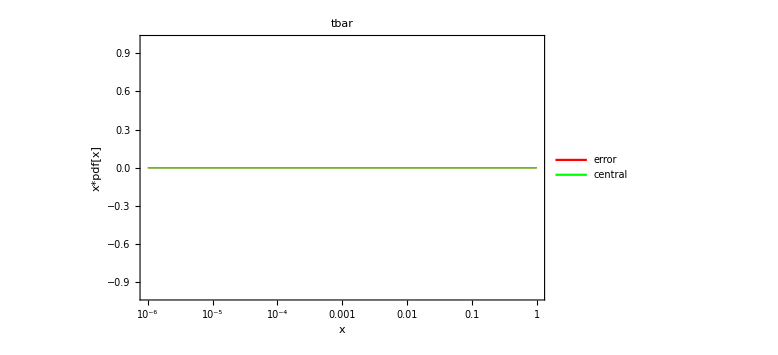

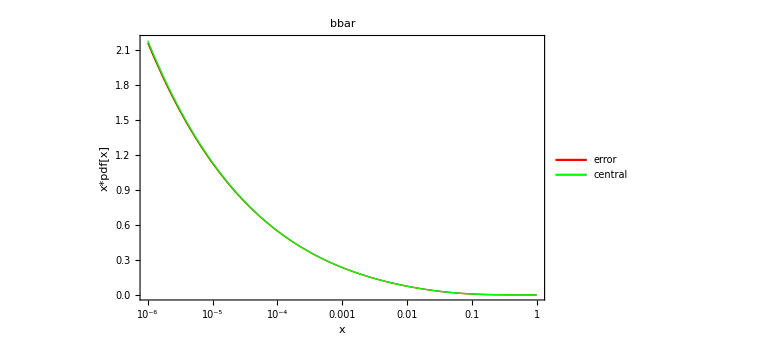

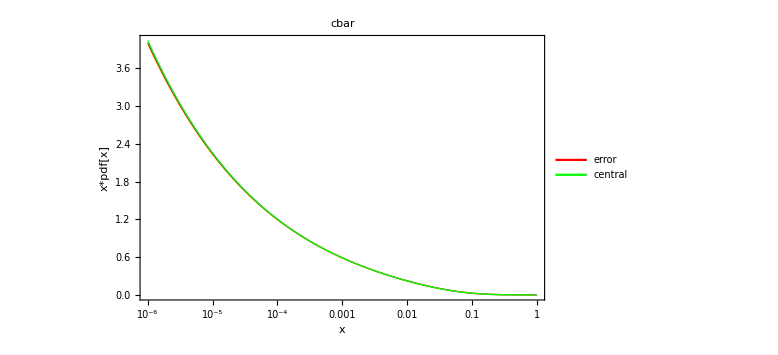

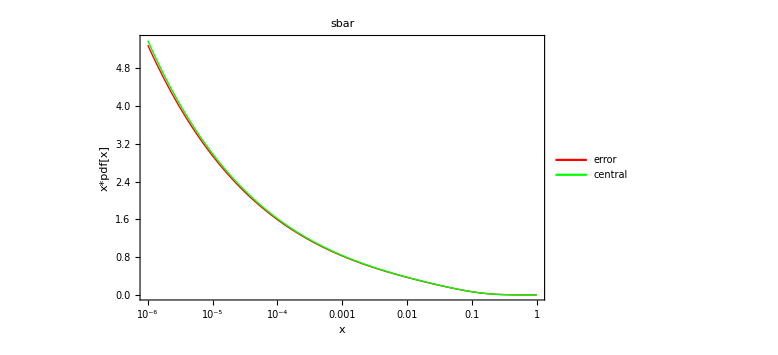

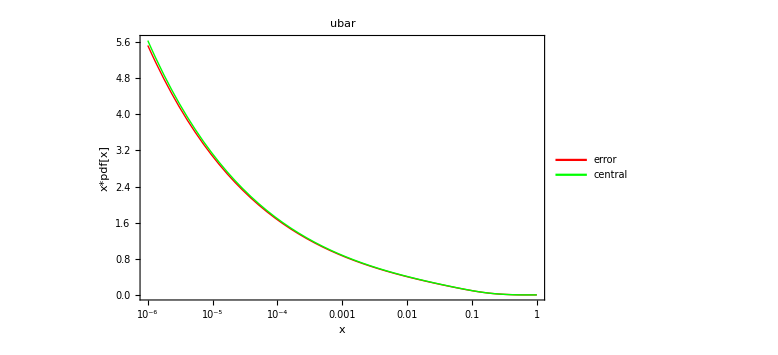

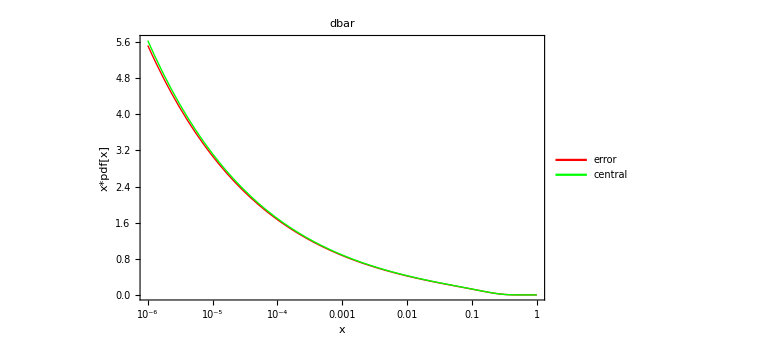

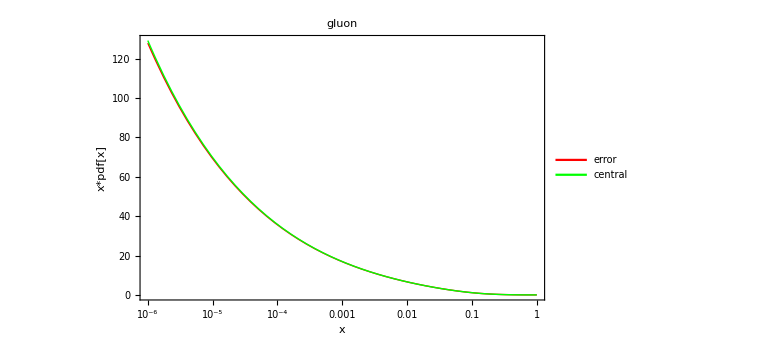

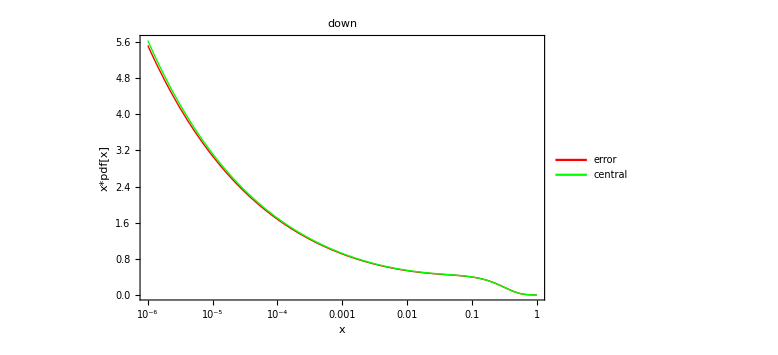

```mathematica
For[i=-6,i≤6,i++,
LogLinearPlot[x {pdf[errorvalue,i,x,q0],pdf[centralvalue,i,x,q0]}//Evaluate ,{x,xMin*100,1},
PlotStyle->{Directive[Red,Thick],Directive[Green,Thick]},
PlotLabel->pdfFlavor[i] ,
FrameLabel->{"x","x*pdf[x]"},
ImageSize->Large,
PlotRange->All,
Frame->True,
BaseStyle->{FontWeight->"Bold",FontSize->12},
GridLines->Automatic,
PlotLegends->Placed[{"error","central"},{0.1,0.18}]] //Print
]
```

## PLAY

#### First we find the minimum value of x for our pdf family.

```mathematica
?pdfXmin
```

```mathematica
xMin=pdfXmin[1]
```

1.×10^-8

```mathematica
pdfQmin[1]
```

pdfQmin[1]

```mathematica
pdfGetInfo[1] //TableForm
```

SetDesc→ "CT10 PDF fits using the standard CTEQ PDF evolution but using the HOPPIT alphas_s running solution. Excluding the D0 Run-II W asymmetry data. mem=0 => central; mem=1-52 => 90% eigenvectors"
SetIndex→10800
Authors→ H.-L.Lai, M.Guzzi, J. Huston, Z.Li, P.M.Nadolsky, J.Pumplin and C.-P.Yuan
Reference→ arXiv:1007.2241
Format→ lhagrid1
DataVersion→4
NumMembers→53
Particle→2212
Flavors→{-5,-4,-3,-2,-1,1,2,3,4,5,21}
OrderQCD→1
ForcePositive→ 1
FlavorScheme→ variable
NumFlavors→5
ErrorType→ hessian
ErrorConfLevel→ 90
XMin→1/100000000
XMax→1
QMin→1.3
QMax→100000
MZ→91.1876
MUp→ 0
MDown→ 0
MStrange→ 0
MCharm→ 1.3
MBottom→ 4.75
MTop→ 172
AlphaS_MZ→ 0.117982
AlphaS_OrderQCD→ 1
AlphaS_Type→ ipol
AlphaS_Qs→{1.3,1.50159,1.75516,2.07811,2.49494,3.04086,3.76712,4.74999,6.23105,8.37433,11.5549,16.4074,24.0385,36.4364,57.3141,91.1876,93.8683,160.657,288.438,545.574,1092.35,2326.49,5300.33,12995.,34515.,100000.}
AlphaS_Vals→{0.39654,0.359977,0.328291,0.300505,0.275891,0.253897,0.234103,0.216597,0.200727,0.18602,0.172381,0.159721,0.147963,0.137042,0.126895,0.117982,0.117468,0.108708,0.100573,0.0930171,0.0860018,0.0794917,0.0734518,0.0678503,0.0626567,0.0578445}
AlphaS_Lambda4→ 0.326
AlphaS_Lambda5→ 0.226

#### We will produce plots of x*pdf(x,Q) for all flavors with the central value in red and the first error set in green. The flavor can be called with the command pdfFlavor[flavor].

```mathematica
q0=1.3;
centralvalue=1;
errorvalue=2;
```

```mathematica
q0=1.3;

For[i=-6,6≤1,i++,
LogLinearPlot[ {pdf[errorvalue,i,x,q0],pdf[centralvalue,i,x,q0]}//Evaluate ,{x,xMin*10^3,1},
PlotStyle->{Directive[Red,Thick],Directive[Green,Thick]},
PlotLabel->pdfFlavor[i] ,
FrameLabel->{"x","pdf[x]"},
ImageSize->Large,
PlotRange->All,
Frame->True,
BaseStyle->{FontWeight->"Bold",FontSize->12},
GridLines->Automatic,
PlotLegends->Placed[{"error","central"},{0.1,0.18}]] //Print
]
```

## Example: Plotting Band Plots

#### Band plots can be created to compare any group of PDF sets.

```mathematica
ct10
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53}

```mathematica
length=ct10 //Length
```

53

```mathematica
(*The following function has been designed to create a LogLinear Plot and modified for appearance sake*)
LHAplot[iset_?IntegerQ,ipart_?IntegerQ,q_]:=
LogLinearPlot[x (pdf[iset,ipart,x,q]),{x,10^-3,0.9},
PlotStyle->Hue[iset/length],
ImageSize->Large,
FrameLabel->{"x","x*pdf[x]"},
Frame->True,
BaseStyle->{FontWeight->"Bold",FontSize->12},
PlotLabel->pdfFlavor[ipart],
PlotRange->All];
```

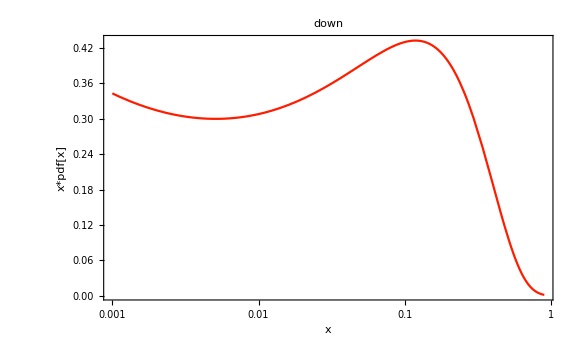

```mathematica
LHAplot[1,1,1.3]
```

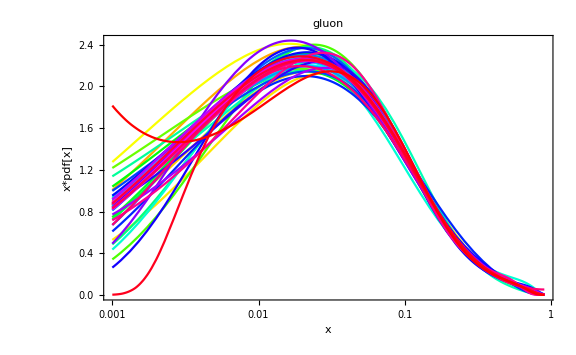

```mathematica
(* These band plots can take a while *)
ipart=0; (* gluon *)
q0=1.3;
bandplot=Table[LHAplot[i,ipart,q0] ,{i,ct10[[1]],length}];
Show[bandplot,PlotRange->All]
```

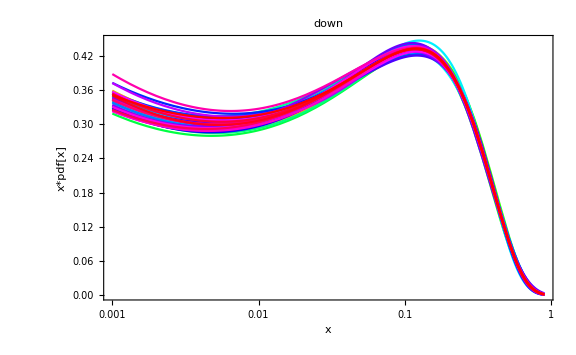

```mathematica
(* These band plots can take a while *)
ipart=1; (* down *)
q0=1.3;
bandplot=Table[LHAplot[i,ipart,q0] ,{i,ct10[[1]],length}];
Show[bandplot,PlotRange->All]
```

## Example : Ratio Plots

#### This compares a value for the same initial variables across all the PDFs in a family

```mathematica
q0=10.;
```

```mathematica
pdfFunction[#, 21, 0.1, q0] & /@ ct10
```

{11.2111,11.2411,11.1835,11.2479,11.1739,11.2892,11.1395,11.584,10.8682,11.2591,11.1483,11.2247,11.2034,11.2734,11.1084,11.1538,11.2646,11.1343,11.25,11.0791,11.2739,11.0974,11.3223,11.4609,10.9436,11.1641,11.3055,11.2178,11.2101,11.2612,11.1734,11.0699,11.3524,11.6641,10.9092,11.1899,11.2257,11.2024,11.2147,11.0661,11.3169,11.2463,11.1828,11.2255,11.1947,11.1695,11.2627,11.042,11.1654,11.2094,11.209,11.2859,11.2088}

#### Here all the PDFs in the family are compared to the central value PDF

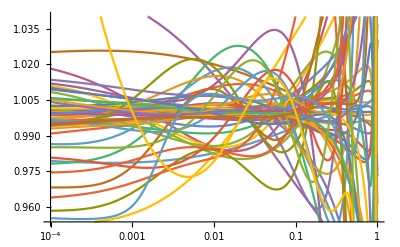

```mathematica
(* These band plots can take a while *)
ratio1=LogLinearPlot[
 Table[pdfFunction[iset, 21, x, q0]/pdfFunction[1, 21, x, q0], {iset, 1, Length[ct10], 1}] // 
  Evaluate, {x, 10.^-4, 1}]
```

## Using pdfGetXlist and pdfGetQlist

#### The x and Q grids can be directly read from the stored PDFs.

```mathematica
iset=1;
```

```mathematica
pdfGetQlist[iset]
```

{{1.3,1.50159,1.75516,2.07811,2.49494,3.04086,3.76712,4.74999,6.23105,8.37433,11.5549,16.4074,24.0385,36.4364,57.3141,93.8684,160.657,288.438,545.574,1092.35,2326.49,5300.33,12995.,34515.,100000.}}

```mathematica
pdfGetXlist[iset]
```

{{1.×10^-8,1.2414×10^-8,1.54112×10^-8,1.9132×10^-8,2.37512×10^-8,2.94855×10^-8,3.66043×10^-8,4.54417×10^-8,5.64127×10^-8,7.00323×10^-8,8.69398×10^-8,1.07929×10^-7,1.33985×10^-7,1.66332×10^-7,2.06486×10^-7,2.56334×10^-7,3.18214×10^-7,3.95031×10^-7,4.90389×10^-7,6.09206×10^-7,7.56249×10^-7,9.38778×10^-7,1.16535×10^-6,1.44661×10^-6,1.79581×10^-6,2.22938×10^-6,2.76764×10^-6,3.43585×10^-6,4.26537×10^-6,5.29516×10^-6,6.57355×10^-6,8.16054×10^-6,0.0000101306,0.0000125762,0.0000156121,0.0000193806,0.0000240586,0.0000298652,0.0000370727,0.0000460185,0.0000571214,0.0000709007,0.0000880003,0.000109218,0.000135543,0.0001682,0.000208704,0.000258931,0.000321196,0.000398359,0.000493945,0.000612291,0.000758725,0.000939771,0.00116349,0.00143942,0.00177935,0.00219741,0.00271045,0.00333846,0.00410484,0.00503669,0.00616486,0.00752468,0.00915177,0.0110878,0.0133759,0.0160562,0.019169,0.0227509,0.0268334,0.0314404,0.0365886,0.0422866,0.0485349,0.0553271,0.0626598,0.0704985,0.0788306,0.087621,0.0968651,0.106525,0.116574,0.126988,0.137743,0.148809,0.160178,0.171817,0.183716,0.19585,0.208205,0.220764,0.233517,0.246449,0.259568,0.272827,0.286233,0.299777,0.313451,0.327248,0.341159,0.355179,0.369295,0.383515,0.397826,0.412222,0.4267,0.441256,0.455884,0.470576,0.485354,0.50018,0.515067,0.530013,0.545014,0.560068,0.575171,0.590323,0.605521,0.620762,0.636045,0.651369,0.66673,0.682126,0.697558,0.713035,0.728531,0.744058,0.759616,0.775202,0.790813,0.806447,0.822102,0.837776,0.853464,0.869163,0.884866,0.900563,0.916236,0.931854,0.947357,0.962579,0.977049,0.989087,0.995616,0.997992,0.998976,0.999487,0.999795,1.}}

#### The pdfXmin function gives the minimum value of x for the set. pdfFunction can only reliably interpolate down to this value.

```mathematica
pdfXmin[iset]
```

1.×10^-8

```mathematica
pdfGetXlist[iset] //Min
```

1.×10^-8

## Additional user functions

### pdfGetInfo function

#### can be used to show what content from the info file has been read into memory

```mathematica
?pdfGetInfo
```

```mathematica
pdfGetInfo[1]//TableForm
```

SetDesc→ "CT10 PDF fits using the standard CTEQ PDF evolution but using the HOPPIT alphas_s running solution. Excluding the D0 Run-II W asymmetry data. mem=0 => central; mem=1-52 => 90% eigenvectors"
SetIndex→10800
Authors→ H.-L.Lai, M.Guzzi, J. Huston, Z.Li, P.M.Nadolsky, J.Pumplin and C.-P.Yuan
Reference→ arXiv:1007.2241
Format→ lhagrid1
DataVersion→4
NumMembers→53
Particle→2212
Flavors→{-5,-4,-3,-2,-1,1,2,3,4,5,21}
OrderQCD→1
ForcePositive→ 1
FlavorScheme→ variable
NumFlavors→5
ErrorType→ hessian
ErrorConfLevel→ 90
XMin→1/100000000
XMax→1
QMin→1.3
QMax→100000
MZ→91.1876
MUp→ 0
MDown→ 0
MStrange→ 0
MCharm→ 1.3
MBottom→ 4.75
MTop→ 172
AlphaS_MZ→ 0.117982
AlphaS_OrderQCD→ 1
AlphaS_Type→ ipol
AlphaS_Qs→{1.3,1.50159,1.75516,2.07811,2.49494,3.04086,3.76712,4.74999,6.23105,8.37433,11.5549,16.4074,24.0385,36.4364,57.3141,91.1876,93.8683,160.657,288.438,545.574,1092.35,2326.49,5300.33,12995.,34515.,100000.}
AlphaS_Vals→{0.39654,0.359977,0.328291,0.300505,0.275891,0.253897,0.234103,0.216597,0.200727,0.18602,0.172381,0.159721,0.147963,0.137042,0.126895,0.117982,0.117468,0.108708,0.100573,0.0930171,0.0860018,0.0794917,0.0734518,0.0678503,0.0626567,0.0578445}
AlphaS_Lambda4→ 0.326
AlphaS_Lambda5→ 0.226

```mathematica
pdfGetInfo[1,"Flavors"]
```

{-5,-4,-3,-2,-1,1,2,3,4,5,21}

### AlphaS functions

```mathematica
alpha=pdfGetInfo[1,"AlphaS_Vals"]
```

{0.39654,0.359977,0.328291,0.300505,0.275891,0.253897,0.234103,0.216597,0.200727,0.18602,0.172381,0.159721,0.147963,0.137042,0.126895,0.117982,0.117468,0.108708,0.100573,0.0930171,0.0860018,0.0794917,0.0734518,0.0678503,0.0626567,0.0578445}

```mathematica
?pdfAlphaS
```

```mathematica
qlist=pdfGetQlist[1](*retrieve qlist from the .dat file*)
```

{{1.3,1.50159,1.75516,2.07811,2.49494,3.04086,3.76712,4.74999,6.23105,8.37433,11.5549,16.4074,24.0385,36.4364,57.3141,93.8684,160.657,288.438,545.574,1092.35,2326.49,5300.33,12995.,34515.,100000.}}

```mathematica
pdfAlphaS[1,Flatten[qlist][[1]]]
```

Created pdfAlphaS for iSet = 1

1 has  1 sub-grid

0.39654

```mathematica
(*For the Q values provided in the .dat file, this checks that the the AlphaS values at those values match those in the .info file*)
(*If they don't match, the alpha value in the info file is dropped. This is done for demonstration purposes*)
For[i=1,i≤Length[Flatten[qlist]],i++,
If[
pdfAlphaS[1,Flatten[qlist][[i]]]≠alpha[[i]],alpha=Drop[alpha,{i}]
]
]
```

```mathematica
tab1=Transpose[{Flatten[qlist],alpha}]
```

{{1.3,0.39654},{1.50159,0.359977},{1.75516,0.328291},{2.07811,0.300505},{2.49494,0.275891},{3.04086,0.253897},{3.76712,0.234103},{4.74999,0.216597},{6.23105,0.200727},{8.37433,0.18602},{11.5549,0.172381},{16.4074,0.159721},{24.0385,0.147963},{36.4364,0.137042},{57.3141,0.126895},{93.8684,0.117468},{160.657,0.108708},{288.438,0.100573},{545.574,0.0930171},{1092.35,0.0860018},{2326.49,0.0794917},{5300.33,0.0734518},{12995.,0.0678503},{34515.,0.0626567},{100000.,0.0578445}}

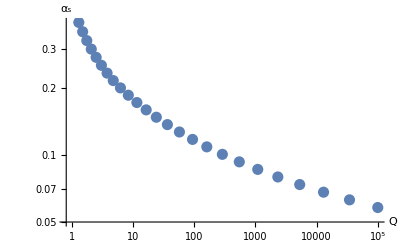

```mathematica
p1=ListLogLogPlot[tab1,AxesLabel->{"Q","α_s"},PlotStyle->{PointSize[.02]}]
```

#### pdfAlphaS function plotting

```mathematica
(*This produces a data set of interpolated AlphaS values*)
tab2={};
e0=Log[10,1.3];
For[ee=e0,ee≤5,ee+=1/5.,
i=10.^ee;
tab2=AppendTo[tab2,{i,pdfAlphaS[1,i]}]
]
```

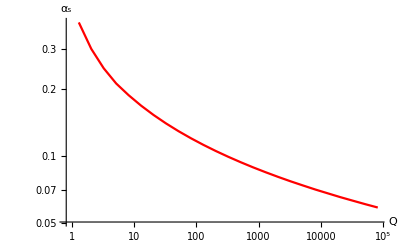

```mathematica
p2=ListLogLogPlot[tab2,PlotRange->Full,AxesLabel->{"Q","α_s"},PlotStyle->{Red},Joined->True]
```

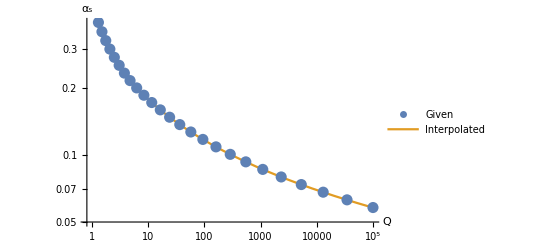

```mathematica
ListLogLogPlot[{tab1,tab2},PlotRange->Full,AxesLabel->{"Q","α_s"},PlotLegends->{"Given","Interpolated"},PlotStyle->{PointSize[.02],PointSize[.005]},Joined->{False,True}]
```

#### The noticeable kink in the 1/AlphaS plot when the b quark turns on is apparent in the plots below

```mathematica
tab={};
For[i=1.3,i≤50,i+=.01,
tab=AppendTo[tab,{i,1/pdfAlphaS[1,i]}]
]
```

```mathematica
p3=ListLogLinearPlot[tab];
```

```mathematica
f1=Fit[Take[tab,-500],{1,Log[x]},x];
f2=Fit[Take[tab,300],{1,Log[x]},x];
```

```mathematica
p4=LogLinearPlot[{f1,f2},{x,1,50},PlotLegends->{"b on","b off"}];
```

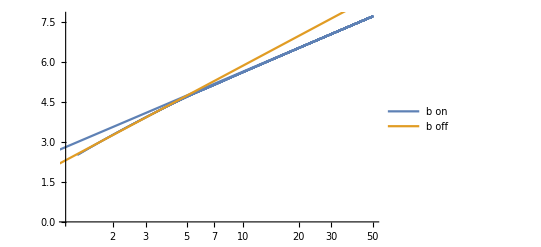

```mathematica
Show[p3,p4]
```

## Example: Change to new PDF family

### This demonstrates how to switch from one PDF family to another

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

```mathematica
pdfSetXpower[1]
```

ManeParse cubic interpolation will be used.

The x-power of the interpolation is set to 1

```mathematica
MSTW=pdfFamilyParseLHA[dirMSTW]
```

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/MSTW2008lo68cl/MSTW2008lo68cl.info.

Included 41 files in the PDF family.

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41}

```mathematica
pdfFunction[#, 0, 0.1, 10.] & /@ MSTW
```

{10.873,10.855,10.883,10.876,10.871,10.849,10.904,10.853,10.885,10.847,10.89,10.904,10.841,10.861,10.882,10.779,10.969,10.844,10.894,10.9,10.838,10.96,10.778,10.813,10.917,10.873,10.875,10.991,10.75,10.826,10.921,10.876,10.873,10.923,10.849,10.87,10.873,10.962,10.766,10.736,10.938}

```mathematica
q0 = 10.;
length=MSTW//Length;
```

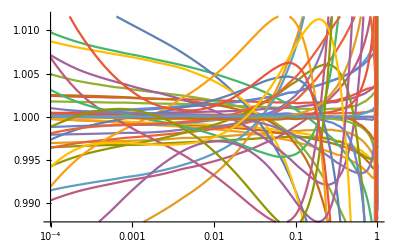

```mathematica
(* These band plots can take a while *)
ratio2=LogLinearPlot[
 Table[pdfFunction[iset, 0, x, q0]/pdfFunction[1, 0, x, q0], {iset, 1,length, 1}] // 
  Evaluate, {x, 10.^-4, 1}]
```

```mathematica
pdfGetInfo[1]//TableForm
```

SetDesc→ "MSTW 2008 LO (68% C.L.).  This set has 41 member PDFs.  mem=0 => central value; mem=1-40 => 20 eigenvectors (+/- directions).  See Section 6 of paper for error calculation.  http://mstwpdf.hepforge.org"
SetIndex→21000
Authors→ A.D. Martin, W.J. Stirling, R.S. Thorne and G. Watt
Reference→ arXiv:0901.0002
Format→ lhagrid1
DataVersion→2
NumMembers→41
Particle→2212
Flavors→{-5,-4,-3,-2,-1,1,2,3,4,5,21}
OrderQCD→0
ForcePositive→ 1
FlavorScheme→ variable
NumFlavors→5
ErrorType→ hessian
XMin→1/1000000
XMax→1
QMin→1
QMax→31622.8
MZ→91.1876
MUp→ 0
MDown→ 0
MStrange→ 0
MCharm→ 1.4
MBottom→ 4.75
MTop→ 1e+10
AlphaS_MZ→ 0.139387
AlphaS_OrderQCD→ 0
AlphaS_Type→ ipol
AlphaS_Qs→{1.,1.11803,1.22475,1.4,1.4,1.58114,1.78885,2.,2.23607,2.52982,2.82843,3.16228,3.4641,4.75,4.75,5.09902,6.32456,8.,10.,12.6491,15.4919,20.,25.2982,31.6228,42.4264,56.5685,74.8332,91.1876,100.,134.164,178.885,236.643,316.228,424.264,565.685,748.332,1000.,1341.64,1788.85,2366.43,3162.28,4242.64,5656.85,7483.32,10000.,13416.4,17888.5,23664.3,31622.8}
AlphaS_Vals→{0.68183,0.614834,0.569141,0.513188,0.513188,0.473939,0.439816,0.41294,0.389161,0.365853,0.347064,0.33011,0.317441,0.280199,0.280199,0.273567,0.255217,0.237814,0.223351,0.209908,0.199546,0.187863,0.178261,0.170009,0.16024,0.151707,0.144236,0.139387,0.137234,0.130797,0.125055,0.119934,0.115053,0.110494,0.106369,0.102641,0.099045,0.0956477,0.0925407,0.0897064,0.0869473,0.0843183,0.0818944,0.0796669,0.0774833,0.0753885,0.0734449,0.0716483,0.0698773}

```mathematica
xlist=pdfGetXlist[1]
```

{{1.×10^-6,2.×10^-6,4.×10^-6,6.×10^-6,8.×10^-6,0.00001,0.00002,0.00004,0.00006,0.00008,0.0001,0.0002,0.0004,0.0006,0.0008,0.001,0.002,0.004,0.006,0.008,0.01,0.014,0.02,0.03,0.04,0.06,0.08,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625,0.65,0.675,0.7,0.725,0.75,0.775,0.8,0.825,0.85,0.875,0.9,0.925,0.95,0.975,1.},{1.×10^-6,2.×10^-6,4.×10^-6,6.×10^-6,8.×10^-6,0.00001,0.00002,0.00004,0.00006,0.00008,0.0001,0.0002,0.0004,0.0006,0.0008,0.001,0.002,0.004,0.006,0.008,0.01,0.014,0.02,0.03,0.04,0.06,0.08,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625,0.65,0.675,0.7,0.725,0.75,0.775,0.8,0.825,0.85,0.875,0.9,0.925,0.95,0.975,1.},{1.×10^-6,2.×10^-6,4.×10^-6,6.×10^-6,8.×10^-6,0.00001,0.00002,0.00004,0.00006,0.00008,0.0001,0.0002,0.0004,0.0006,0.0008,0.001,0.002,0.004,0.006,0.008,0.01,0.014,0.02,0.03,0.04,0.06,0.08,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625,0.65,0.675,0.7,0.725,0.75,0.775,0.8,0.825,0.85,0.875,0.9,0.925,0.95,0.975,1.}}

#### Note for MSTW grids, the .dat file is divided into multiple sections based on Q value, thus extra inputs maybe required.

```mathematica
?pdfNumQpartition
```

```mathematica
pdfNumQpartition[1]
```

3

```mathematica
qlist=pdfGetQlist[1,3]
```

pdfGetQlist[1,3]

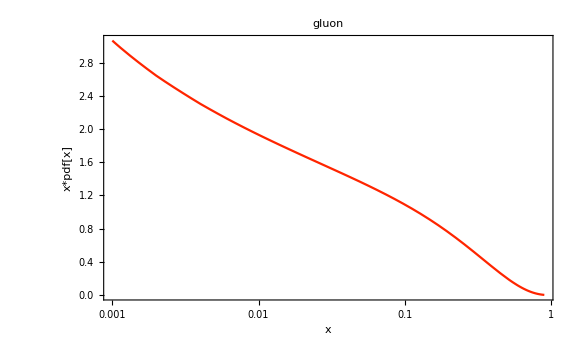

```mathematica
LHAplot[1,0,1.3]
```

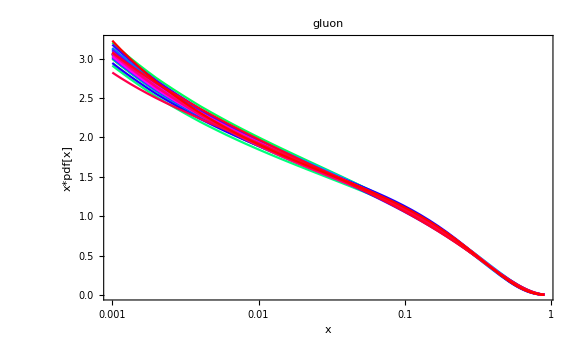

```mathematica
ipart=0; (* GLUON *)
q0=1.3;
bandplot=Table[LHAplot[i,ipart,q0] ,{i,MSTW[[1]],length}];
Show[bandplot,PlotRange->All]
```

### Working with multiple families at once.

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

```mathematica
MSTW=pdfFamilyParseLHA[dirMSTW]
ct10=pdfFamilyParseLHA[dirCT10]
nnpdf=pdfFamilyParseLHA[dirNNPDF]
```

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/MSTW2008lo68cl/MSTW2008lo68cl.info.

Included 41 files in the PDF family.

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41}

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/CT10/CT10.info.

Included 53 files in the PDF family.

{42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94}

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/NNPDF30_nlo_as_0118/NNPDF30_nlo_as_0118.info.

Included 101 files in the PDF family.

{95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195}

```mathematica
total=pdfSetList//Length
```

195

```mathematica
Join[MSTW,ct10,nnpdf]//Length
```

195

#### Check sum rule:

```mathematica
Off[NIntegrate::izero]
Off[NIntegrate::ncvb]
q0=2.0;
iset0=1;(*MSTW*)
```

```mathematica
tab= Table[ NIntegrate[  x*pdf[iset0,ipart,x,q0],{x,0,1}],{ipart,-5,5,1}];
Plus @@ tab
```

0.998711

```mathematica
flavorlist={};
```

```mathematica
For[i=-5,i≤5,i++,AppendTo[flavorlist,pdfFlavor[i]];]
```

```mathematica
flavorlist
```

{bbar,cbar,sbar,ubar,dbar,gluon,down,up,strange,charm,bottom}

```mathematica
{Range[-5,5],flavorlist,Round[100 tab]} //Transpose //Grid[#,Frame->All]&
```

-5 | bbar | 0
-4 | cbar | 0
-3 | sbar | 1
-2 | ubar | 3
-1 | dbar | 4
0 | gluon | 43
1 | down | 15
2 | up | 31
3 | strange | 1
4 | charm | 0
5 | bottom | 0

#### Check sum rule:

```mathematica
Off[NIntegrate::izero]
Off[NIntegrate::ncvb]
q0=2.0;
iset0=total-(Length[nnpdf])+1;(*nnpdf*)
```

```mathematica
tab= Table[ NIntegrate[  x*pdf[iset0,ipart,x,q0],{x,0,1}],{ipart,-5,5,1}];
Plus @@ tab
```

1.00187

```mathematica
flavorlist={};
```

```mathematica
For[i=-5,i≤5,i++,AppendTo[flavorlist,pdfFlavor[i]];]
```

```mathematica
flavorlist
```

{bbar,cbar,sbar,ubar,dbar,gluon,down,up,strange,charm,bottom}

```mathematica
{Range[-5,5],flavorlist,Round[100 tab]} //Transpose //Grid[#,Frame->All]&
```

-5 | bbar | 0
-4 | cbar | 0
-3 | sbar | 1
-2 | ubar | 3
-1 | dbar | 4
0 | gluon | 43
1 | down | 15
2 | up | 31
3 | strange | 2
4 | charm | 0
5 | bottom | 0

## PDS Files

### Here we demonstrate the ability to handle PDS files in addition to LHA files

```mathematica
pdfReset[]
```

Default Mathematica interpolator will be used.

All internal variables have been reset.

```mathematica
ct10pds=pdfFamilyParseCTEQ[dirCT10pds]
```

General::munfl: 5.91609/(1.×10^315) is too small to represent as a normalized machine number; precision may be lost.

/home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/PDS/ct10.pds/ct10.35.pds was not initialized: 2 error messages

Included 52 files in the PDF family.

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52}

```mathematica
CTEQ66=pdfFamilyParseCTEQ[dirCTEQ66]
```

Included 45 files in the PDF family.

{53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97}

```mathematica
pdfFunction[1,1,.1,10]
```

3.96968

```mathematica
Clear[pdf]
pdf[iset_?IntegerQ,ipart_?IntegerQ,x_?NumericQ,q_?NumericQ]:=pdfFunction[iset,ipart,x,q]
```

```mathematica
pdf[1,1,.1,10]
pdf[2,1,0.1,10]

centralvalue = 1;

pdf[centralvalue,1,0.1,10]
```

3.96968

3.95809

3.96968

#### Check sum rule:

```mathematica
Off[NIntegrate::izero]
Off[NIntegrate::ncvb]
q0=2.0;
iset0=1;
```

```mathematica
tab= Table[ NIntegrate[ x pdf[iset0,ipart,x,q0],{x,0,1}],{ipart,-5,5,1}];
Plus @@ tab
```

0.999837

```mathematica
flavorlist={};
```

```mathematica
For[i=-5,i≤5,i++,AppendTo[flavorlist,pdfFlavor[i]];]
```

```mathematica
flavorlist
```

{bbar,cbar,sbar,ubar,dbar,gluon,down,up,strange,charm,bottom}

```mathematica
{Range[-5,5],flavorlist,Round[100 tab]} //Transpose //Grid[#,Frame->All]&
```

-5 | bbar | 0
-4 | cbar | 0
-3 | sbar | 2
-2 | ubar | 3
-1 | dbar | 4
0 | gluon | 42
1 | down | 15
2 | up | 32
3 | strange | 2
4 | charm | 0
5 | bottom | 0

#### Check sum rule:

```mathematica
Off[NIntegrate::izero]
Off[NIntegrate::ncvb]
q0=2.0;
iset0=Length[pdfSetList]-Length[CTEQ66]+1;(*CTEQ66*)
```

```mathematica
tab= Table[ NIntegrate[ x pdf[iset0,ipart,x,q0],{x,0,1}],{ipart,-5,5,1}];
Plus @@ tab
```

0.99984

```mathematica
flavorlist={};
```

```mathematica
For[i=-5,i≤5,i++,AppendTo[flavorlist,pdfFlavor[i]];]
```

```mathematica
flavorlist
```

{bbar,cbar,sbar,ubar,dbar,gluon,down,up,strange,charm,bottom}

```mathematica
{Range[-5,5],flavorlist,Round[100 tab]} //Transpose //Grid[#,Frame->All]&
```

-5 | bbar | 0
-4 | cbar | 0
-3 | sbar | 2
-2 | ubar | 3
-1 | dbar | 4
0 | gluon | 42
1 | down | 15
2 | up | 31
3 | strange | 2
4 | charm | 0
5 | bottom | 0

### Compare PDS and LHA files

#### Here we compare the CT10 PDF family in both the LHA and PDS formats. As expected, they yield the same results.

```mathematica
ct10LHA=pdfFamilyParseLHA[dirCT10]
```

Successfully read /home/olness/Dropbox/mp/ManeParse5_DEMO/FOR WEB/ManeParse5_Demo/./PDFDIR/LHA/CT10/CT10.info.

Included 53 files in the PDF family.

{98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150}

```mathematica
q0=10;
centralvaluePDS=1;
centralvalueLHA=Length[pdfSetList]-Length[ct10LHA]+1;
```

```mathematica
pdf[centralvalueLHA,1,.1,1.5]
```

4.28504

```mathematica
pdf[centralvaluePDS,1,.1,1.5]
```

4.28504

```mathematica
xMin=Max[pdfXmin[centralvaluePDS],pdfXmin[centralvalueLHA]];
```

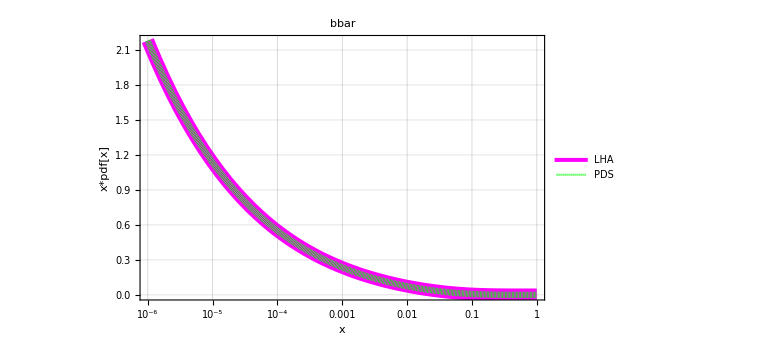

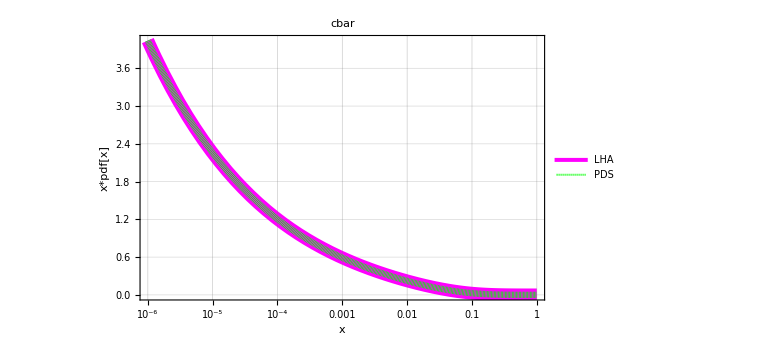

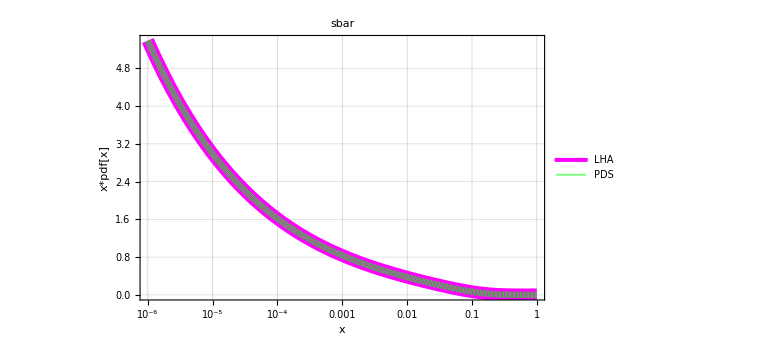

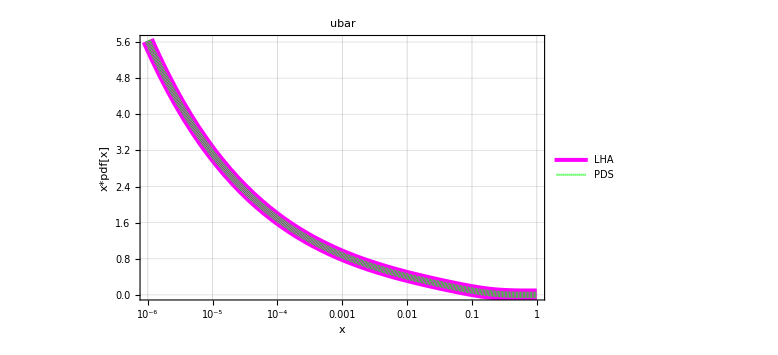

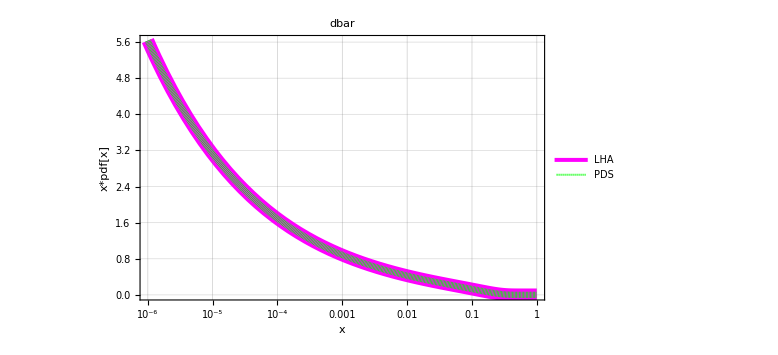

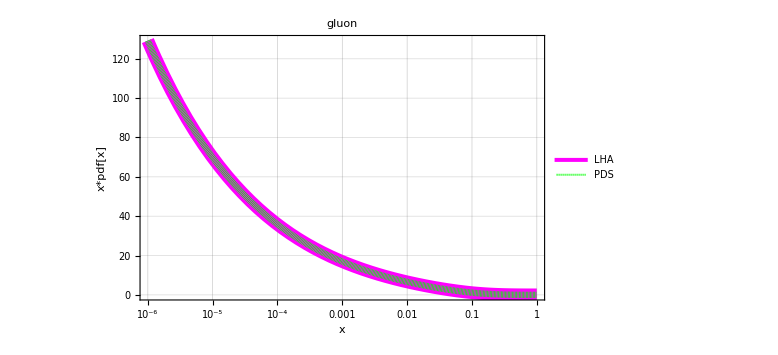

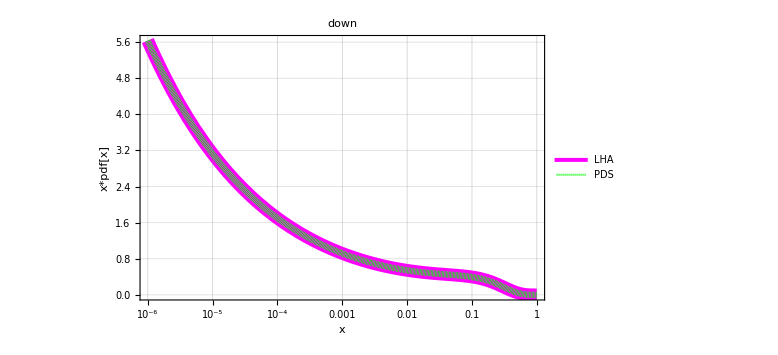

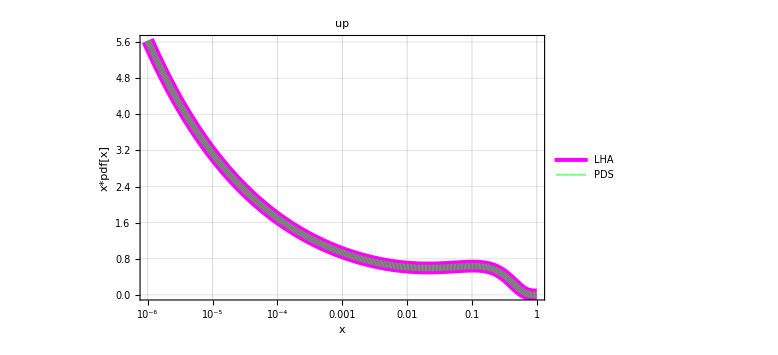

```mathematica
For[i=-5,i≤5,i++,
LogLinearPlot[x {pdf[centralvaluePDS,i,x,q0],pdf[centralvalueLHA,i,x,q0]}//Evaluate ,{x,xMin*100,1},
PlotStyle->{Directive[Magenta,Thickness[0.016]],Directive[Green,Thickness[0.008],Dashing[.0]]},
PlotLabel->pdfFlavor[i] ,
FrameLabel->{"x","x*pdf[x]"},
ImageSize->Large,
PlotRange->All,
Frame->True,
BaseStyle->{FontWeight->"Bold",FontSize->12},
GridLines->Automatic,
PlotLegends->Placed[{"LHA","PDS"},{0.1,0.18}]] //Print
]
```